# Mattis-Bardeen theory

## frequency dependent complex normalized optical conductivity for superconductors

-Graphics--Graphics--Graphics--Graphics-
From, Martin Dressel, George Grüner-Electrodynamics of solids_ optical properties of electrons in matter-Cambridge University Press (2002) -Prashant Chauhan

Sept 29th, 2017
Notes : The  parameters and constants are as follows: T = temperature, w = frequency (f), e = energy, d = Δ(T), d0 = Δ(0), suitable units would be milli electron volts .,
Sigma1s and sigma2s are real and img part of complex conductivity. We write planck constant h = 4.135667662/10^12 meV.s x  10^12 to convert it to THz units; so ‘w’ will be in THz. You can assign data folder for data transfer at the bottom of the page. 
X = cos (θ), Y = sin (θ) so Usadel Equation: i*e*X + d0*Y-n*d0*XY==0; F(e, e+hw) =  Re[Y[e]]*Re[Y[e+hw]] + Im[X[e]]*Im[X[e+hw]]; I take E_g = d[T]

```mathematica
k=8.6173303/10^2;d0=0.8;Tc=4.1;(*h=4.135667662/10^12 meV.s*) h= 4.135667662;T=3.5; 3.5*k*Tc
```

1.23659

functions:

Approximate form of superconducting gap:

```mathematica
d[T_]:=d0*Tanh[1.74*√(Tc/T-1)]
```

```mathematica
(*d[T1_]:=Quiet[(2 d1 d0)/1.76/.FindRoot[NIntegrate[Tanh[(√(x^2+d1^2))/T1]/(√(x^2+d1^2)),{x,0,12.3611}]==1/0.3,{d1,1}]];*) (*Exact form for superconducting gap*)
```

Function for solving the MB equations and finding Re and Im part of normalised conductance for a given T, Tc and Δ:

```mathematica
f[m_]:=1/(ⅇ^(m/(k T))+1)
K[w_,e_]:=Abs[e^2+h w e+d[T]^2]/(√((e+h w)^2-d[T]^2))
A[w_,e_]:=((f[e]-f[e+h w]) K[w,e])/(√(e^2-d[T]^2))
B[w_,e_]:=((1-2 f[e+h w]) K[w,e])/(√(e^2-d[T]^2))
B2[w_,e_]:=((1-2 f[e+h w]) K[w,e])/(√(d[T]^2-e^2))
intA[w_]:=NIntegrate[A[w,e],{e,d[T],1000 *d[T]},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13]
intB[w_]:=Piecewise[{{0,h w<2 d[T]},{NIntegrate[B[w,e],{e,d[T]-h w,-d[T]},Method->{"GaussKronrodRule","GaussPoints"->12},MaxRecursion->18,WorkingPrecision->10],h w≥2 d[T]}}]
sigma1s[w_]:=(2 intA[w]+intB[w])/(h w)
sigma2s[w_]:=Piecewise[{{NIntegrate[B2[w,e]/(h w),{e,d[T]-h w,d[T]},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13],h w≤2 *d[T]},{NIntegrate[B2[w,e]/(h w),{e,- d[T],d[T]},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13],h w>2*d[T]}}]
```

Testing code :

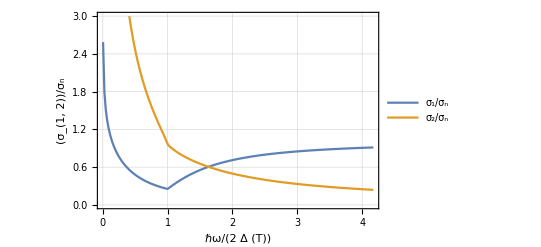

```mathematica
T=3.5; data=Table[{h*w/(2*d[T]),sigma1s[w]},{w,0.001,1,0.005}] ;(*ListPlot[{data},PlotRange->All,Joined->True]*)
data1=Table[{h*w/(2*d[T]),sigma2s[w]},{w,0.001,1,0.005}] ;
ListPlot[{data,data1},PlotRange->{{0,3}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω/(2  Δ (T))","(σ_(1, 2))/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"σ_1/σ_n","σ_2/σ_n"}]
(*data = Prepend[data, {X,Y}];*)(*Export["sigma1s.dat",data];Export["sigma2s.dat",data1];*)
```

Setting directory for exporting/import data.

```mathematica
SetDirectory["F:\\OneDrive - Johns Hopkins University\\Project\\thz\\Beta-Tungsten\\Mathematica"]
```

F:\OneDrive - Johns Hopkins University\Project\thz\Beta-Tungsten\Mathematica

Importing expt data & Generating and plotting data along with experimental data : BiNi+MgO/Ni+MgO_sigma1 and sigma2
Note: Always run below codes together to avoid loading wrong data.

```mathematica
BM=Import["Temp_dep_norm6K_Data_.txt", "Table"];(*BM2 = Import["", "Table"];*)
m = Dimensions[BM][[1]]; m50=Table[{BM[[i,1]],BM[[i,2]]},{i,2,m,1}];m45=Table[{BM[[i,1]],BM[[i,3]]},{i,2,m,1}];m35=Table[{BM[[i,1]],BM[[i,4]]},{i,2,m,1}];m30=Table[{BM[[i,1]],BM[[i,5]]},{i,2,m,1}]; m16 = Table[{BM[[i,1]],BM[[i,6]]},{i,2,m,1}];
```

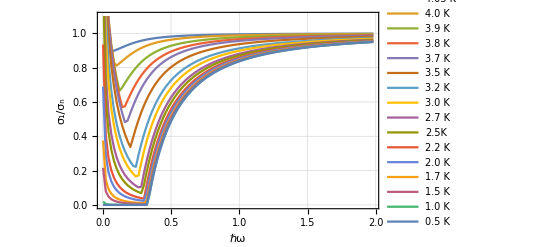

```mathematica
d0=0.68;T=4.05; data=Table[{w,sigma1s[w]},{w,0.002,2,0.02}] ;T = 4.0; data40 =Table[{w,sigma1s[w]},{w,0.002,2,0.02}] ;T = 3.9; data39 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 3.8; data38 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 3.7; data37 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 3.5; data35 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 3.2; data32 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 3.0; data30 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 2.7; data27 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 2.5; data25 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 2.2; data22 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 2.0; data20 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 1.7; data17 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 1.5; data15 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];T = 1.0; data10 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 0.5; data05 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
ListPlot[{data,data40, data39, data38, data37, data35,data32, data30,data27, data25,data22, data20,data17, data15,data10, data05},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"4.05 K","4.0 K","3.9 K","3.8 K","3.7 K", "3.5 K","3.2 K","3.0 K","2.7 K","2.5K","2.2 K","2.0 K", "1.7 K","1.5 K","1.0 K","0.5 K"}, Background->White]
```

```mathematica
Solve[ En x*ⅈ+A √(1-x^2)-B x √(1-x^2)==0,x]
```

```mathematica
roo =N[ x/.Solve[ⅈ 0.2 x+0.25 √(1-x^2)-0.0025 x √(1-x^2)==0,x]]
```

{-1.62165,180.001}

```mathematica
ro[e_,d_,n_]:={x,y}/.FindRoot[{e*x*ⅈ+d* y-d*n* x y==0,x^2+y^2==1},{{x,0.5},{y,0.5}}]
```

```mathematica
ro[0.23,0.25,0.25]
```

{0.830601+0.906533 ⅈ,1.22796-0.613183 ⅈ}

```mathematica
Re[ro[0.23,0.25,0.1]⟦1⟧]
```

1.21065

Code for LARKIN - OVCHINNIKOV MODEL:

Below section has constants.After that line 1) Function to calculate the solutions of Usadel equation : i*E*sin(θ) + Δ*cos(θ) - n*Δ*sin(θ)cos(θ) == 0; Δ is the tunneling gap. We can take, Y = cos(θ), X = sin(θ);  F (e, e + hw) = Re[Y[e]]Re[Y[e + hw]] + Im[X[e]]Im[X[e + hw]]; I take optical gap, Eg[T] = Δ[T]*(1-n^(2/3))^(3/2).

```mathematica
Δ=0.424;n=0.1;Tc = 4.5; k=8.6173303/10^2; h= 4.135667662;
```

```mathematica
U[en_]:=N[{x,y}/.FindRoot[{-(Δ1 n x y)+Δ1 y+ⅈ en x==0,x^2+y^2==1},{{x,0.5},{y,0.5}}]]
f[m_]:=1/(ⅇ^(m/(k T))+1)
FC[w_,en_]:=Abs[UC[en] UC[en+h w]+US[en] US[en+h w]]
M1[w_,en_]:=(f[en]-f[en+h w]) FC[w,en]
M2[w_,en_]:=(1-2 f[en+h w]) FC[w,en]
intM1[w_]:=NIntegrate[M1[w,en],{en,Δ,200 Δ},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13]
intM2[w_]:=Piecewise[{{0,h w<2 Δ},{NIntegrate[M2[w,en],{en,Δ-h w,-Δ},Method->{"GaussKronrodRule","GaussPoints"->12},MaxRecursion->18,WorkingPrecision->10],h w≥2 Δ}}]
σ1[w_]:=(2 intM1[w]+intM2[w])/(h w)
```

```mathematica
n= 0.1; Δ1 = 0.8; U[0.7]
```

{1.38614+1.24556 ⅈ,1.43876-1.2 ⅈ}

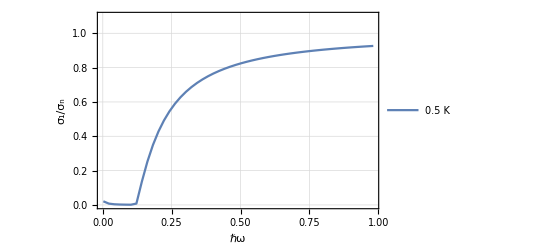

```mathematica
T = 0.5; dat = Table[{w,σ1[w]},{w,0.002,1,0.02}];
ListPlot[{dat},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"0.5 K"}, Background->White]
```

```mathematica
UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,50,0.01}]]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,50,0.01}]]
```

InterpolatingFunction[{{-50., 50.}}, <>]

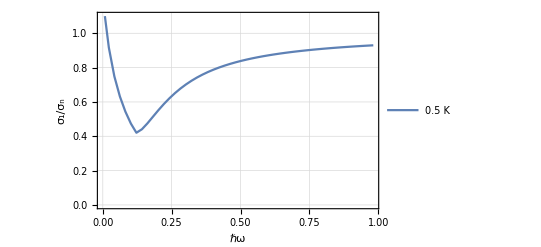

```mathematica
T = 3.0; dat = Table[{w,σ1[w]},{w,0.002,1,0.02}];
ListPlot[{dat},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"0.5 K"}, Background->White]
```

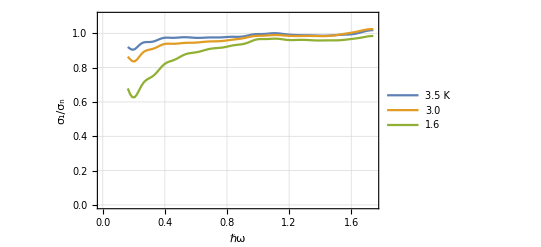

```mathematica
ListPlot[{m35,m30,m16},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"3.5 K", "3.0", "1.6"}, Background->White]
```

```mathematica
Δ=0.424;n=0.5;Tc = 4.2;
```

```mathematica
UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,50,0.01}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,50,0.01}]]
```

InterpolatingFunction[{{-50., 50.}}, <>]

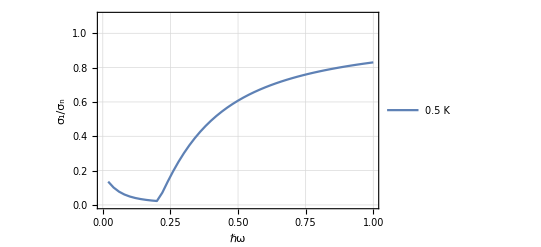

```mathematica
T = 1.6; dat = Table[{w,σ1[w]},{w,0.02,1,0.02}];
ListPlot[{dat},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"0.5 K"}, Background->White]
```

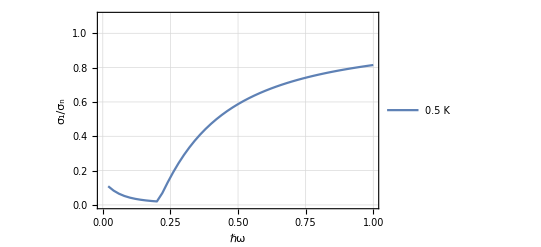

```mathematica
T = 1.6; dat = Table[{w,σ1[w]},{w,0.02,1,0.02}];
ListPlot[{dat},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"0.5 K"}, Background->White]
```

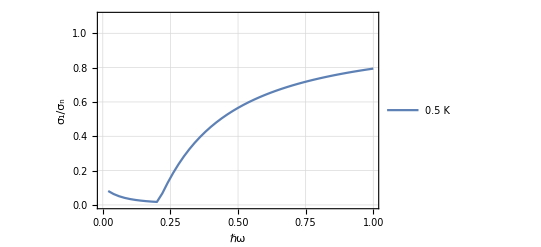

```mathematica
Δ=0.424;n=1;Tc = 4.2;UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,50,0.01}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,50,0.01}]];
T = 1.6; dat = Table[{w,σ1[w]},{w,0.02,1,0.02}];
ListPlot[{dat},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"0.5 K"}, Background->White]
```

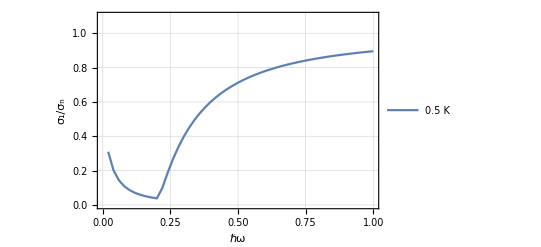

```mathematica
Δ=0.424;n=0.01;Tc = 4.2;UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -100,100,0.01}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -100,100,0.01}]];
T = 1.6; dat = Table[{w,σ1[w]},{w,0.02,1,0.02}];
ListPlot[{dat},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"0.5 K"}, Background->White]
```

```mathematica
Tc=4.2; d0=0.424;
T=4.1; data=Table[{w,sigma1s[w]},{w,0.02,1,0.02}] ;T = 3.9; data39 = Table[{w,sigma1s[w]},{w,0.002,1,0.02}];
T = 3.5; data35 = Table[{w,sigma1s[w]},{w,0.02,1,0.02}];
T = 3.0; data30 = Table[{w,sigma1s[w]},{w,0.02,1,0.02}];T = 2.7; data27 = Table[{w,sigma1s[w]},{w,0.002,1,0.02}];
T = 1.6; data16 = Table[{w,sigma1s[w]},{w,0.02,1,0.02}];
ListPlot[{data,data39,data35,data30,data27,data16},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"4.05 K","3.9 K", "3.5 K","3.0 K","2.7 K","1.6K"}, Background->White]
```

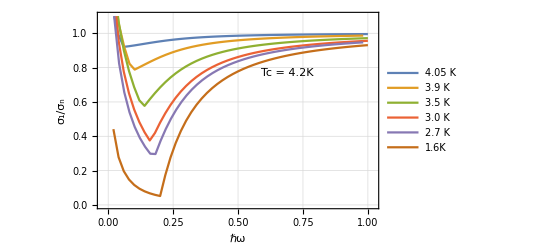

```mathematica
Tc = 4.2;Δ=0.422;n=0.5;Δ1=Δ (1-n^(2/3))^(-3/2);UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,200,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,200,0.02}]];
T = 1.6; dat = Table[{w,σ1[w]},{w,0.02,2,0.02}]; d0=Δ1;
dat1p6=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
ListPlot[{dat, dat1p6},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"1.6 K_LO", "1.6 K_MB"}, Background->White]
```

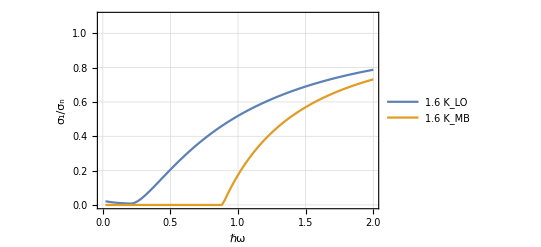

```mathematica
ListPlot[{dat, dat1p6},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"1.6 K_LO", "1.6 K_MB"}, Background->White]
```

```mathematica
2*0.422/(4.2*k)
```

2.33196

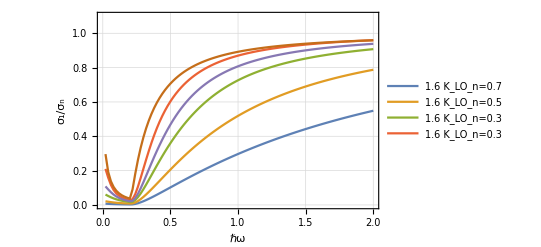

```mathematica
Tc = 4.2;Δ=0.422;n=0.7;Δ1=Δ (1-n^(2/3))^(-3/2);UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,200,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,200,0.02}]];
T = 1.6; datp7 = Table[{w,σ1[w]},{w,0.02,2,0.02}]; d0=Δ1;datp7mb=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
n=0.3;Δ1=Δ (1-n^(2/3))^(-3/2);UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,200,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,200,0.02}]];
datp3 = Table[{w,σ1[w]},{w,0.02,2,0.02}]; d0=Δ1;datp3mb=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
n=0.1;Δ1=Δ (1-n^(2/3))^(-3/2);UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,200,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,200,0.02}]];
datp1 = Table[{w,σ1[w]},{w,0.02,2,0.02}]; d0=Δ1;datp1mb=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
n=0.2;Δ1=Δ (1-n^(2/3))^(-3/2);UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,200,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,200,0.02}]];
datp2 = Table[{w,σ1[w]},{w,0.02,2,0.02}]; d0=Δ1;datp2mb=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
n=0.;Δ1=Δ (1-n^(2/3))^(-3/2);UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,200,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,200,0.02}]];
datp0 = Table[{w,σ1[w]},{w,0.02,2,0.02}]; d0=Δ1;datp0mb=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
ListPlot[{datp7,dat,datp3,datp1,datp2, datp0 },PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"1.6 K_LO_n=0.7","1.6 K_LO_n=0.5","1.6 K_LO_n=0.3", "1.6 K_LO_n=0.3" }, Background->White]
```

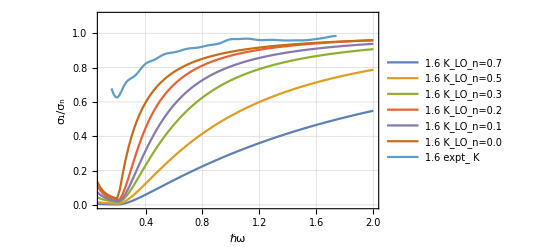

```mathematica
ListPlot[{datp7,dat,datp3,datp1,datp2, datp0, m16},PlotRange->{{0.1,2},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->{"1.6 K_LO_n=0.7","1.6 K_LO_n=0.5","1.6 K_LO_n=0.3", "1.6 K_LO_n=0.2" , "1.6 K_LO_n=0.1" ,"1.6 K_LO_n=0.0" , expt_1.6 K}, Background->White]
```

```mathematica
ListPlot[{datp7,datp7mb, m16},PlotRange->{{0.1,1.8},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->Placed[{"1.6 K_LO_n=0.7","1.6 K_mb_Δ=4.33 meV" , "expt_1.6 K"},None], Background->White]
```

Placed::labpos: None is not a valid position for the placement of labels.

```mathematica
ListPlot[{dat,dat1p6, m16},PlotRange->{{0.1,1.8},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->Placed[{"1.6 K_LO_n=0.5","1.6 K_mb_Δ=1.87 meV" , "expt_1.6 K"},None], Background->White]
```

Placed::labpos: None is not a valid position for the placement of labels.

```mathematica
ListPlot[{datp3,datp3mb, m16},PlotRange->{{0.1,1.8},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->Placed[{"1.6 K_LO_n=0.3","1.6 K_mb_Δ=1.02 meV" , "expt_1.6 K"},None], Background->White]
```

Placed::labpos: None is not a valid position for the placement of labels.

```mathematica
ListPlot[{datp2,datp2mb, m16},PlotRange->{{0.1,1.8},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->Placed[{"1.6 K_LO_n=0.2","1.6 K_mb_Δ=0.79 meV" , "expt_1.6 K"},None], Background->White]
```

Placed::labpos: None is not a valid position for the placement of labels.

```mathematica
ListPlot[{datp1,datp1mb, m16},PlotRange->{{0.1,1.8},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->Placed[{"1.6 K_LO_n=0.1","1.6 K_mb_Δ=0.61 meV" , "expt_1.6 K"}, None], Background->White]
```

Placed::labpos: None is not a valid position for the placement of labels.

```mathematica
ListPlot[{datp0,datp0mb, m16},PlotRange->{{0.1,1.8},{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends->Placed[{"1.6 K_LO_n=0","1.6 K_mb_Δ=0.422 meV" , "expt_1.6 K"},None], Background->White]
```

Placed::labpos: None is not a valid position for the placement of labels.

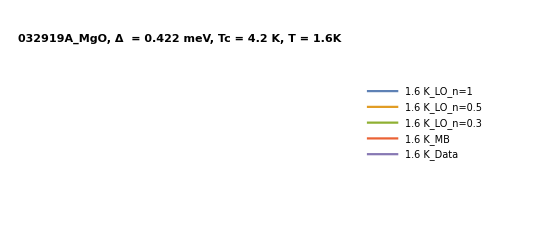

```mathematica
Δ=1.902;n=0.01508;Tc = 11.6;UC = Interpolation[Table[{en, Re[U[en]⟦2⟧]},{en, -50,400,0.02}]];US = Interpolation[Table[{en, Im[U[en]⟦1⟧]},{en, -50,400,0.02}]];
T = 1.6; dat1p6lo = Table[{w,σ1[w]},{w,0.02,2,0.02}];
```

```mathematica
Tc=11.6; d0=2.09;
T=1.6; dat1p6=Table[{w,sigma1s[w]},{w,0.02,2,0.02}] ;
```

```mathematica
ListPlot[{dat1p6lo,dat1p6},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> Placed[{"1.6 K_LO_n=0.015","1.6 K_MB"},None], Background->White]
```

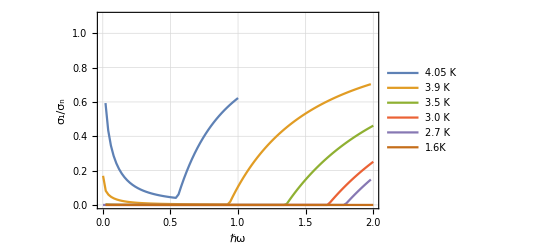

```mathematica
Tc=4.2; d0=4.3;
T=4.1; data=Table[{w,sigma1s[w]},{w,0.02,1,0.02}] ;T = 3.9; data39 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 3.5; data35 = Table[{w,sigma1s[w]},{w,0.02,2,0.02}];
T = 3.0; data30 = Table[{w,sigma1s[w]},{w,0.02,2,0.02}];T = 2.7; data27 = Table[{w,sigma1s[w]},{w,0.002,2,0.02}];
T = 1.6; data16 = Table[{w,sigma1s[w]},{w,0.02,2,0.02}];
ListPlot[{data,data39,data35,data30,data27,data16},PlotRange->{{0,1.1}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed],Frame-> True, FrameLabel->{"ℏω","σ_1/σ_n"},LabelStyle->Directive[Black,Bold],FrameStyle->Directive[Black,12],PlotLegends-> {"4.05 K","3.9 K", "3.5 K","3.0 K","2.7 K","1.6K"}, Background->White]
```

```mathematica
2*0.422/(4.2*k)
```

2.33196